```mathematica
Clear[coord,metric,inversemetric,affine,riemann,ricci,scalar,einstein,r,θ,ϕ,t]
```

```mathematica
n=4
```

4

```mathematica
coord={t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
metric={{-ⅇ^ψ[r],0,0,0},{0,1/(1-b[r]/r),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}}
```

{{-ⅇ^ψ[r],0,0,0},{0,1/(1-b[r]/r),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}}

```mathematica
metric//MatrixForm
```

(-ⅇ^ψ[r] | 0 | 0 | 0
0 | 1/(1-b[r]/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{-ⅇ^(-ψ[r]),0,0,0},{0,1-b[r]/r,0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}}

```mathematica
inversemetric//MatrixForm
```

(-ⅇ^(-ψ[r]) | 0 | 0 | 0
0 | 1-b[r]/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2)

```mathematica
affine:=affine=Simplify[Table[0.5*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[affine[[i,j,k]]=!=0,{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | 0.
Γ[1, 2, 1] | 0.5 ψ'[r]
Γ[1, 2, 2] | 0.
Γ[1, 3, 1] | 0.
Γ[1, 3, 2] | 0.
Γ[1, 3, 3] | 0.
Γ[1, 4, 1] | 0.
Γ[1, 4, 2] | 0.
Γ[1, 4, 3] | 0.
Γ[1, 4, 4] | 0.
Γ[2, 1, 1] | (0.5 ⅇ^ψ[r] (r-1. b[r]) ψ'[r])/r
Γ[2, 2, 1] | 0.
Γ[2, 2, 2] | (-0.5 b[r]+0.5 r b'[r])/(r (r-1. b[r]))
Γ[2, 3, 1] | 0.
Γ[2, 3, 2] | 0.
Γ[2, 3, 3] | -1. r+1. b[r]
Γ[2, 4, 1] | 0.
Γ[2, 4, 2] | 0.
Γ[2, 4, 3] | 0.
Γ[2, 4, 4] | -1. (r-1. b[r]) Sin[θ]^2
Γ[3, 1, 1] | 0.
Γ[3, 2, 1] | 0.
Γ[3, 2, 2] | 0.
Γ[3, 3, 1] | 0.
Γ[3, 3, 2] | 1./r
Γ[3, 3, 3] | 0.
Γ[3, 4, 1] | 0.
Γ[3, 4, 2] | 0.
Γ[3, 4, 3] | 0.
Γ[3, 4, 4] | -1. Cos[θ] Sin[θ]
Γ[4, 1, 1] | 0.
Γ[4, 2, 1] | 0.
Γ[4, 2, 2] | 0.
Γ[4, 3, 1] | 0.
Γ[4, 3, 2] | 0.
Γ[4, 3, 3] | 0.
Γ[4, 4, 1] | 0.
Γ[4, 4, 2] | 1./r
Γ[4, 4, 3] | 1. Cot[θ]
Γ[4, 4, 4] | 0.

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]*affine[[i,k,s]]-affine[[s,j,k]]*affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 1, 2, 1] | 0.
R[1, 1, 3, 1] | 0.
R[1, 1, 3, 2] | 0.
R[1, 1, 4, 1] | 0.
R[1, 1, 4, 2] | 0.
R[1, 1, 4, 3] | 0.
R[1, 2, 2, 1] | 0.-(0.25 (-1. b[r]+1. r b'[r]) ψ'[r])/(r (r-1. b[r]))+0.25 ψ'[r]^2+0.5 ψ''[r]
R[1, 2, 3, 1] | 0.
R[1, 2, 3, 2] | 0.
R[1, 2, 4, 1] | 0.
R[1, 2, 4, 2] | 0.
R[1, 2, 4, 3] | 0.
R[1, 3, 2, 1] | 0.
R[1, 3, 3, 1] | 0.+(0.5 r-0.5 b[r]) ψ'[r]
R[1, 3, 3, 2] | 0.
R[1, 3, 4, 1] | 0.
R[1, 3, 4, 2] | 0.
R[1, 3, 4, 3] | 0.
R[1, 4, 2, 1] | 0.
R[1, 4, 3, 1] | 0.
R[1, 4, 3, 2] | 0.
R[1, 4, 4, 1] | 0.5 (r-1. b[r]) Sin[θ]^2 ψ'[r]
R[1, 4, 4, 2] | 0.
R[1, 4, 4, 3] | 0.
R[2, 1, 2, 1] | (ⅇ^ψ[r] (b[r] (0.25 ψ'[r]-0.25 r ψ'[r]^2-0.5 r ψ''[r])+r (-0.25 b'[r] ψ'[r]+0.25 r ψ'[r]^2+0.5 r ψ''[r])))/r^2
R[2, 1, 3, 1] | 0.
R[2, 1, 3, 2] | 0.
R[2, 1, 4, 1] | 0.
R[2, 1, 4, 2] | 0.
R[2, 1, 4, 3] | 0.
R[2, 2, 2, 1] | 0.
R[2, 2, 3, 1] | 0.
R[2, 2, 3, 2] | 0.
R[2, 2, 4, 1] | 0.
R[2, 2, 4, 2] | 0.
R[2, 2, 4, 3] | 0.
R[2, 3, 2, 1] | 0.
R[2, 3, 3, 1] | 0.
R[2, 3, 3, 2] | (0.5 b[r])/r-0.5 b'[r]
R[2, 3, 4, 1] | 0.
R[2, 3, 4, 2] | 0.
R[2, 3, 4, 3] | 0.
R[2, 4, 2, 1] | 0.
R[2, 4, 3, 1] | 0.
R[2, 4, 3, 2] | 0.
R[2, 4, 4, 1] | 0.
R[2, 4, 4, 2] | (Sin[θ]^2 (0.5 b[r]-0.5 r b'[r]))/r
R[2, 4, 4, 3] | 0.
R[3, 1, 2, 1] | 0.
R[3, 1, 3, 1] | (0.5 ⅇ^ψ[r] (r-1. b[r]) ψ'[r])/r^2
R[3, 1, 3, 2] | 0.
R[3, 1, 4, 1] | 0.
R[3, 1, 4, 2] | 0.
R[3, 1, 4, 3] | 0.
R[3, 2, 2, 1] | 0.
R[3, 2, 3, 1] | 0.
R[3, 2, 3, 2] | 0.+(-0.5 b[r]+0.5 r b'[r])/(r^2 (r-1. b[r]))
R[3, 2, 4, 1] | 0.
R[3, 2, 4, 2] | 0.
R[3, 2, 4, 3] | 0.
R[3, 3, 2, 1] | 0.
R[3, 3, 3, 1] | 0.
R[3, 3, 3, 2] | 0.
R[3, 3, 4, 1] | 0.
R[3, 3, 4, 2] | 0.
R[3, 3, 4, 3] | 0.
R[3, 4, 2, 1] | 0.
R[3, 4, 3, 1] | 0.
R[3, 4, 3, 2] | 0.
R[3, 4, 4, 1] | 0.
R[3, 4, 4, 2] | 0.
R[3, 4, 4, 3] | -(1. b[r] Sin[θ]^2)/r
R[4, 1, 2, 1] | 0.
R[4, 1, 3, 1] | 0.
R[4, 1, 3, 2] | 0.
R[4, 1, 4, 1] | (0.5 ⅇ^ψ[r] (r-1. b[r]) ψ'[r])/r^2
R[4, 1, 4, 2] | 0.
R[4, 1, 4, 3] | 0.
R[4, 2, 2, 1] | 0.
R[4, 2, 3, 1] | 0.
R[4, 2, 3, 2] | 0.
R[4, 2, 4, 1] | 0.
R[4, 2, 4, 2] | 0.+(-0.5 b[r]+0.5 r b'[r])/(r^2 (r-1. b[r]))
R[4, 2, 4, 3] | 0.
R[4, 3, 2, 1] | 0.
R[4, 3, 3, 1] | 0.
R[4, 3, 3, 2] | 0.
R[4, 3, 4, 1] | 0.
R[4, 3, 4, 2] | 0.
R[4, 3, 4, 3] | 0.+(1. b[r])/r
R[4, 4, 2, 1] | 0.
R[4, 4, 3, 1] | 0.
R[4, 4, 3, 2] | 0.
R[4, 4, 4, 1] | 0.
R[4, 4, 4, 2] | 0.
R[4, 4, 4, 3] | 0.

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (ⅇ^ψ[r] ((-0.75 b[r]+r (1.-0.25 b'[r])) ψ'[r]+r (0.25 r-0.25 b[r]) ψ'[r]^2+r (0.5 r-0.5 b[r]) ψ''[r]))/r^2
R[2, 1] | 0.
R[2, 2] | 0.+(-1. b[r]+1. r b'[r])/(r^2 (r-1. b[r]))+(0.25 (-1. b[r]+1. r b'[r]) ψ'[r])/(r (r-1. b[r]))-0.25 ψ'[r]^2-0.5 ψ''[r]
R[3, 1] | 0.
R[3, 2] | 0.
R[3, 3] | 0.+(0.5 b[r])/r+0.5 b'[r]+(-0.5 r+0.5 b[r]) ψ'[r]
R[4, 1] | 0.
R[4, 2] | 0.
R[4, 3] | 0.
R[4, 4] | (Sin[θ]^2 (r (0.5 b'[r]-0.5 r ψ'[r])+b[r] (0.5+0.5 r ψ'[r])))/r

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]*ricci[[i,j]],{i,1,n},{j,1,n}]]
```

0.-(2. (1. r^2-1.75 r b[r]+0.75 b[r]^2) ψ'[r])/(r^2 (1. r-1. b[r]))-(0.5 (1. r^2-2. r b[r]+1. b[r]^2) ψ'[r]^2)/(r (1. r-1. b[r]))+(0.5 b'[r] (b[r] (-4.-1. r ψ'[r])+r (4.+1. r ψ'[r])))/(r^2 (r-1. b[r]))-1. ψ''[r]+(1. b[r] ψ''[r])/(1. r-1. b[r])-(1. b[r]^2 ψ''[r])/(1. r^2-1. r b[r])

```mathematica
einstein:=einstein=Simplify[ricci-0.5*scalar*metric]
```

```mathematica
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}]
```

G[1, 1] | (ⅇ^ψ[r] b'[r])/r^2
G[2, 1] | 0.
G[2, 2] | 0.+(1. r ψ'[r])/(1. r-1. b[r])^2+(-0.25+(0.25 r^2)/(1. r-1. b[r])^2) ψ'[r]^2-0.5 ψ''[r]+(0.5 r ψ''[r])/(r-1. b[r])-(0.5 b[r] (2.+4. r ψ'[r]+1. r^2 ψ'[r]^2+1. r^2 ψ''[r]))/(r (1. r-1. b[r])^2)+(0.25 b[r]^2 (4.+4. r ψ'[r]+1. r^2 ψ'[r]^2+2. r^2 ψ''[r]))/(r^2 (1. r-1. b[r])^2)
G[3, 1] | 0.
G[3, 2] | 0.
G[3, 3] | 0.+(0.5 b[r])/r+0.5 b'[r]+(-0.5 r+0.5 b[r]) ψ'[r]-0.5 r^2 (0.-(2. (1. r^2-1.75 r b[r]+0.75 b[r]^2) ψ'[r])/(r^2 (1. r-1. b[r]))-(0.5 (1. r^2-2. r b[r]+1. b[r]^2) ψ'[r]^2)/(r (1. r-1. b[r]))+(0.5 b'[r] (b[r] (-4.-1. r ψ'[r])+r (4.+1. r ψ'[r])))/(r^2 (r-1. b[r]))-1. ψ''[r]+(1. b[r] ψ''[r])/(1. r-1. b[r])+(1. b[r]^2 ψ''[r])/(-1. r^2+1. r b[r]))
G[4, 1] | 0.
G[4, 2] | 0.
G[4, 3] | 0.
G[4, 4] | (Sin[θ]^2 (r b[r] (0.5-0.75 r ψ'[r]-0.5 r^2 ψ'[r]^2+b'[r] (0.5+0.25 r ψ'[r])-1. r^2 ψ''[r])+b[r]^2 (-0.5+0.25 r ψ'[r]+0.25 r^2 ψ'[r]^2+0.5 r^2 ψ''[r])+r^2 (b'[r] (-0.5-0.25 r ψ'[r])+r (0.5 ψ'[r]+0.25 r ψ'[r]^2+0.5 r ψ''[r]))))/(r (1. r-1. b[r]))

```mathematica
u={ⅇ^(-0.5*ψ[r]),0,0,0}
```

{ⅇ^(-0.5 ψ[r]),0,0,0}

```mathematica
T:=Simplify[(ρ[r]+P[r])* Outer[Times,u,u]+P[r] *inversemetric]
```

```mathematica
T//MatrixForm
```

(-ⅇ^(-ψ[r]) P[r]+ⅇ^(-1. ψ[r]) (P[r]+ρ[r]) | 0 | 0 | 0
0 | ((r-b[r]) P[r])/r | 0 | 0
0 | 0 | P[r]/r^2 | 0
0 | 0 | 0 | (Csc[θ]^2 P[r])/r^2)

```mathematica
T1=metric.T.metric
```

{{ⅇ^(2 ψ[r]) (-ⅇ^(-ψ[r]) P[r]+ⅇ^(-1. ψ[r]) (P[r]+ρ[r])),0,0,0},{0,((r-b[r]) P[r])/(r (1-b[r]/r)^2),0,0},{0,0,r^2 P[r],0},{0,0,0,r^2 P[r] Sin[θ]^2}}

```mathematica
T1//MatrixForm
```

(ⅇ^(2 ψ[r]) (-ⅇ^(-ψ[r]) P[r]+ⅇ^(-1. ψ[r]) (P[r]+ρ[r])) | 0 | 0 | 0
0 | ((r-b[r]) P[r])/(r (1-b[r]/r)^2) | 0 | 0
0 | 0 | r^2 P[r] | 0
0 | 0 | 0 | r^2 P[r] Sin[θ]^2)

```mathematica
covariantT:=Simplify[Table[D[T[[i,ν]],coord[[ν]]]+Sum[affine[[i,ν,s]] T[[s,ν]]+affine[[ν,ν,s]] T[[i,s]],{s,1,n}],{i,1,n},{ν,1,n}]]
```

```mathematica
covariantT//TableForm
```

0. | 0. | 0. | 0.
(0.5 ((1. r-1. b[r]) P[r]+(1. r-1. b[r]) ρ[r]) ψ'[r])/r | 0.+((r-b[r]) P'[r])/r | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.

```mathematica
covariantT=FullSimplify[covariantT]
```

{{0.,0.,0.,0.},{((0.5 r-0.5 b[r]) (P[r]+ρ[r]) ψ'[r])/r,0.+((r-b[r]) P'[r])/r,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
NonZeroEntries=Total[Flatten[FullSimplify[covariantT]]]
```

0.+((r-b[r]) P'[r])/r+((0.5 r-0.5 b[r]) (P[r]+ρ[r]) ψ'[r])/r

```mathematica
NonZeroEntries
```

0.+((r-b[r]) P'[r])/r+((0.5 r-0.5 b[r]) (P[r]+ρ[r]) ψ'[r])/r

```mathematica
Eqn=NonZeroEntries==0
```

0.+((r-b[r]) P'[r])/r+((0.5 r-0.5 b[r]) (P[r]+ρ[r]) ψ'[r])/r==0

```mathematica
EFE1=(ⅇ^ψ[r] b'[r])/r^2==8*π*ⅇ^ψ[r]*ρ[r]
```

(ⅇ^ψ[r] b'[r])/r^2==8 ⅇ^ψ[r] π ρ[r]

```mathematica
Solve[EFE1,ρ[r]]
```

{{ρ[r]→b'[r]/(8 π r^2)}}

```mathematica
FullSimplify[+(r ψ'[r])/(r- b[r])^2+(-0.25+(0.25 r^2)/( r- b[r])^2) ψ'[r]^2-0.5 ψ''[r]+(0.5 r ψ''[r])/(r- b[r])-(0.5 b[r] (2+4 r ψ'[r]+ r^2 ψ'[r]^2+r^2 ψ''[r]))/(r ( r- b[r])^2)+(0.25 b[r]^2 (4+4 r ψ'[r]+ r^2 ψ'[r]^2+2 r^2 ψ''[r]))/(r^2 ( r- b[r])^2)]
```

(b[r] (-1. r+1. b[r])+r (1. r^2-2. r b[r]+1. b[r]^2) ψ'[r])/(r^2 (r-1. b[r])^2)

```mathematica
Simplify[(b[r] (- r+ b[r])+r (r^2-2 r b[r]+ b[r]^2) ψ'[r])/(r^2 (r- b[r])^2)]
```

(r^2 ψ'[r]-b[r] (1+r ψ'[r]))/(r^2 (r-b[r]))

```mathematica
EFE2=(r^2 ψ'[r]-b[r] (1+r ψ'[r]))/(r^2 (r-b[r]))==8*π*((r-b[r]) P[r])/(r (1-b[r]/r)^2)
```

(r^2 ψ'[r]-b[r] (1+r ψ'[r]))/(r^2 (r-b[r]))==(8 π (r-b[r]) P[r])/(r (1-b[r]/r)^2)

```mathematica
Solve[EFE2,P[r]]
```

{{P[r]→(-b[r]+r^2 ψ'[r]-r b[r] ψ'[r])/(8 π r^3)}}

```mathematica
Eos=P[r]==μ*ρ[r]
```

P[r]==μ ρ[r]

```mathematica
Eos/. {μ->-2}
```

P[r]==-2 ρ[r]

```mathematica
Eqn
```

0.+((r-b[r]) P'[r])/r+((0.5 r-0.5 b[r]) (P[r]+ρ[r]) ψ'[r])/r==0

```mathematica
Eqn1=Eqn/.{P[r]->-2*ρ[r],P'[r]->D[-2*ρ[r],r]}
```

0.-(2 (r-b[r]) ρ'[r])/r-((0.5 r-0.5 b[r]) ρ[r] ψ'[r])/r==0

```mathematica
Eqn1
```

0.-(2 (r-b[r]) ρ'[r])/r-((0.5 r-0.5 b[r]) ρ[r] ψ'[r])/r==0

```mathematica
Eqn2=Eqn1/.{ρ[r]->b'[r]/(8 π r^2),ρ'[r]->D[b'[r]/(8 π r^2),r]}
```

0.-((0.5 r-0.5 b[r]) b'[r] ψ'[r])/(8 π r^3)-(2 (r-b[r]) (-b'[r]/(4 π r^3)+b''[r]/(8 π r^2)))/r==0

```mathematica
Eqn3=Eqn2/.{ψ'[r]->0}
```

0.-(2 (r-b[r]) (-b'[r]/(4 π r^3)+b''[r]/(8 π r^2)))/r==0

```mathematica
Eqn4=Simplify[Eqn3]
```

((r-b[r]) (-2 b'[r]+r b''[r]))/r==0

```mathematica
Sol=Quiet[DSolve[{((r-b[r]) *(-2* b'[r]+r* b''[r]))/r==0,b[0]==0,b'[1]==8π},b[r],r],DSolve::bvnul]
```

{{b[r]→(8 π r^3)/3}}

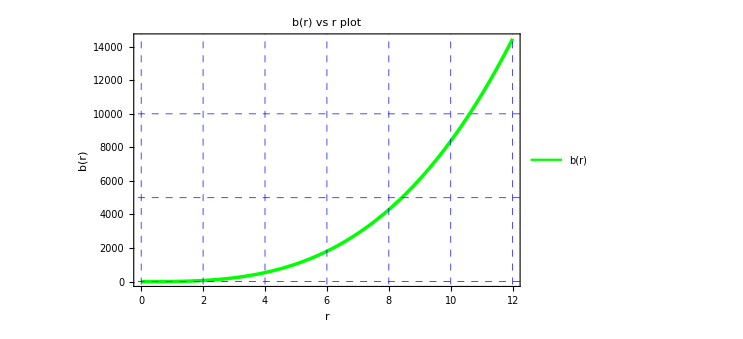

```mathematica
Plot[b[r] /. Sol,{r,0,12},PlotStyle->{Green,Thickness[0.0045]},PlotLegends->Placed[LineLegend[{"b(r)"},LegendLayout->"Column",LegendFunction->"Panel"],{0.87,0.1}],Frame->True,FrameStyle->Directive[Brown,Thick],FrameLabel->{Style["r",Bold,30,Black],Style["b(r)",Bold,30,Black]},PlotLabel->Style["b(r) vs r plot",Bold,20,Blue],LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->{Directive[Blue,17],(*Bottom ticks*)Directive[Red,17],(*Left ticks*)Directive[Brown,17],(*Top ticks*)Directive[Black,17]},(*Right ticks*)FrameTicks->{(*Bottom ticks*){{0,2,4,6,8,10,12},None},(*Left ticks*){{0,5000,10000,15000},None},(*Top ticks*){{0,2,4,6,8,10,12},None},(*Right ticks*){{0,5000,10000,15000},None}},ImageSize->{550,350},GridLines->{{0,2,4,6,8,10,12},{0,5000,10000,15000}},GridLinesStyle->Directive[Blue,Dashed]]
```